```mathematica
α=7.297352533 10^-3;
H[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1+π(λ[y,β] x)/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
H0[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1) Exp[-(2y)/β];
dH[x_,y_,β_]:=((x+(2 *x -1))/(2*x^2*(1-x)) √(x/(1-x))ArcTan[ √(x/(1-x))]+(π(1-λ[y,β])^2 λ[y,β])/((1-λ[y,β]^2-x)^2))Exp[-(2y)/β];
u1[y_,β_]:=(2 β^2)/(α^2 y^2)*Exp[ExpIntegralEi[-(2y)/β]];
λ[y_,β_]:= α/2 (Log[4.5 u1[y,β]]-2.44 Log[Log[0.15 u1[y,β]]]);
LDis1=Table[x/.FindRoot[x-y+H0[x,y,200],{x,0.9999,0.99999},MaxIterations->1000],{y,0,100,0.1}];
```

```mathematica
LDis2=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.99999},MaxIterations->1000],{y,0.0000000001,80,0.1}];
```

```mathematica
LDis22={0.08290201632109075,0.16385235233435635,0.242349990972648,0.317941419438368,0.39013185236360565,0.45838932792499343,0.5221698630223364,0.5809617618530176,0.6343456220230954,0.682058776639578,0.7240453758299448,0.7604731871233416,0.7917091081156463,0.8182619838908367,0.8407126440097589,0.8596508783194002,0.8756305642293666,0.8891447012044094,0.9006163616312193,0.9103999234513827,0.9187877205224687,0.9260187790028825,0.932287705731374,0.9377527788743424,0.9425428854167701,0.9467632668162161,0.9505001803875462,0.9538246359603222,0.9567953720660589,0.9594612200319731,0.9618629814391978,0.9640349213725574,0.9660059592485472,0.9678006217508954,0.9694398084281153,0.9709414094286001,0.9723208061706711,0.9735912789951952,0.9747643406094522,0.9758500100864763,0.9768570390288654,0.9777930990801174,0.978664938058738,0.9794785105138234,0.9802390873378239,0.9809513481599663,0.9816194595233456,0.9822471412776672,0.9828377231653342,0.9833941932156086,0.9839192392704322,0.9844152847310326,0.9848845194248715,0.9853289263386535,0.9857503048364407,0.9861502908900144,0.9865303747275193,0.9868919163111526,0.9872361589049261,0.987564241019849,0.9878772069463121,0.9881760160576543,0.988461551138662,0.9887346255207232,0.9889959898004288,0.9892463375392654,0.9894863104714077,0.9897165031434239,0.9899374670729502,0.9901497144827676,0.9903537216592567,0.9905499319780655,0.9907387586342165,0.9909205871094682,0.991095777405495,0.9912646660681055,0.9914275680246607,0.9915847782542409,0.9917365733078318,0.9918832126938121,0.9920249401422884,0.992161984760308,0.9922945620778275,0.9924228750677137,0.9925471149347249,0.992667462019527,0.9927840865112346,0.9928971491387949,0.9930068018063837,0.9931131881780854,0.9932164442176694,0.9933166986866032,0.993414073604878,0.9935086846772794,0.9936006416882285,0.9936900488678055,0.9937770052313539,0.9938616048948355,0.9939439373679122,0.9940240878265448,0.9941021373667444,0.9941781632409609,0.9942522390784659,0.9943244350983883,0.9943948182759524,0.9944634525560573,0.9945303990004568,0.9945957159493285,0.9946594591681713,0.9947216819854263,0.9947824354214891,0.9948417683074513,0.9948997274097521,0.9949563575157275,0.9950117015533376,0.995065800677682,0.9951186943594266,0.9951704204696513,0.9952210153579955,0.995270513926775,0.9953189497010573,0.9953663548943128,0.9954127604698515,0.9954581962055897,0.9955026907365127,0.9955462716207647,0.995588965381203,0.9956307975593639,0.995671792749158,0.9957119746491703,0.995751366098038,0.9957899891128901,0.9958278649253112,0.9958650140153427,0.9959014561438853,0.9959372103832845,0.995972295146521,0.9960067282122986,0.9960405267639445,0.9960737073905053,0.9961062861326696,0.9961382784960544,0.9961696994738523,0.9962005635675786,0.9962308848066977,0.9962606767673533,0.9962899525899631,0.9963187249966178,0.9963470063069231,0.9963748084536248,0.9964021429973701,0.9964290211408157,0.9964554537421111,0.9964814513277852,0.9965070241050661,0.9965321819736642,0.9965569345370435,0.9965812911132061,0.9966052607450194,0.9966288522100994,0.9966520740302797,0.9966749344806816,0.9966974415984078,0.9967196031908742,0.9967414268437993,0.9967629199288679,0.9967840896110817,0.9968049428558151,0.9968254864355844,0.9968457269360358,0.9968656707646865,0.9968853241521596,0.9969046931623202,0.9969237836954888,0.9969426014965039,0.9969611521547583,0.9969794411142123,0.996997473675542,0.9970152550014412,0.9970327901207117,0.9970500839326908,0.9970671412110341,0.9970839666081397,0.9971005646584031,0.9971169397820809,0.9971330962889124,0.9971490383810351,0.9971647701572044,0.997180295614438,0.9971956186524594,0.9972107430759027,0.9972256725972732,0.9972404108396602,0.997254961339349,0.9972693275483321,0.9972835128367177,0.9972975204970932,0.9973113537407964,0.99732501570746,0.9973385094629966,0.9973518380025598,0.9973650042525355,0.9973780110724669,0.9973908612569161,0.9974035575372635,0.9974161025834491,0.9974284990056548,0.997440749355931,0.9974528561297668,0.9974648217676044,0.997476648657577,0.9974883391328883,0.9974998954783698,0.9975113199288097,0.9975226146709262,0.997533781844629,0.9975448235442426,0.99755574181969,0.9975665386775486,0.9975772160825224,0.9975877759580049,0.9975982201874574,0.9976085506153456,0.9976187690481246,0.9976288772551947,0.9976388769698294,0.9976487698900759,0.9976585576796282,0.9976682419686765,0.99767782435473,0.9976873064034166,0.9976966896492608,0.9977059755964367,0.9977151657195016,0.997724261464108,0.9977332642476954,0.9977421754601622,0.9977509964645203,0.9977597285975287,0.9977683731703126,0.9977769314689626,0.9977854047551191,0.9977937942665399,0.9978103268000912,0.9978184721832195,0.9978265385146388,0.997834526920683,0.9978424385068997,0.9978502743585197,0.997858035540912,0.9978657231000286,0.9978733380628372,0.9978808814377413,0.9978883542149909,0.9978957573671721,0.9979030918491495,0.9979103585989318,0.9979175585391467,0.997924692573819,0.9979317615928831,0.9979387664699871,0.9979457080637167,0.9979525872177454,0.9979594047611382,0.9979661615086749,0.9979728582611448,0.99797949580563,0.9979860749157713,0.9979925963528411,0.9979990608636726,0.9980054691837645,0.9980118220359423,0.9980181201309581,0.9980243641677364,0.9980305548336164,0.9980366928045855,0.9980427787455112,0.9980488133103655,0.9980547971424486,0.9980607308746089,0.9980666151294695,0.998072450518836,0.9980782376463243,0.9980839771045458,0.9980896694770167,0.9980953153379666,0.9981009152525178,0.9981064697768629,0.9981119794584363,0.9981174448360808,0.9981228664402072,0.998128244792943,0.9981335804086366,0.9981388737930168,0.9981441254445342,0.9981493358538427,0.9981545055040866,0.9981596348710416,0.9981647244232514,0.9981797587712378,0.9981846936099651,0.9981895908728217,0.9981944509876927,0.9981992743761146,0.9982040614533911,0.9982088126287055,0.9982135283052314,0.9982182088802406,0.9982228547452093,0.9982274662859213,0.9982320438825697,0.9982365879098563,0.9982410987370877,0.998245576728272,0.9982500222422112,0.9982544356325923,0.9982588172480769,0.9982631674323885,0.9982674865243985,0.9982717748582103,0.9982760327632406,0.9982802605643011,0.9982844585816767,0.9982886271312033,0.998292766524343,0.998296877068259,0.9983009590658878,0.9983050128160106,0.9983090386133239,0.9983130367485069,0.9983170075082891,0.9983209511755079,0.9983248680292155,0.9983287583446565,0.9983326223934158,0.9983364604434367,0.9983402727590884,0.9983440596012253,0.9983478212272436,0.9983515578911385,0.9983552698435579,0.998358957331858,0.9983626206001553,0.9983662598893795,0.9983698754373237,0.9983734674786947,0.9983770362451632,0.9983805819654101,0.9983841048651759,0.9983876051673053,0.998391083091594,0.998394538855679,0.9983979726737352,0.9984013847574768,0.9984047753159423,0.9984081445555361,0.9984114926800691,0.998414819890799,0.9984181263864697,0.9984214123633488,0.9984246780152674,0.9984279235336554,0.998431149107579,0.9984343549237766,0.9984375411666939,0.9984407080185179,0.9984438556592118,0.9984469842665474,0.9984500940161394,0.9984531850814754,0.9984562576339494,0.9984593118428922,0.9984623478756014,0.9984653658973724,0.9984683660715272,0.9984713485594432,0.9984743135205822,0.998477261112518,0.9984801914909641,0.9984831048098005,0.9984860012211,0.9984888808750476,0.998491743920439,0.9984945905039129,0.9984974207705771,0.998500234863857,0.9985030329255189,0.9985058150956952,0.9985085815129076,0.9985113323140892,0.9985140676346085,0.9985167876082901,0.9985194923674375,0.9985221820428536,0.9985327924719248,0.9985354086396624,0.9985380104781344,0.9985405981082055,0.9985431716493661,0.9985457312199251,0.9985482769366604,0.9985508089152554,0.998553327270005,0.9985558321140185,0.9985583235591337,0.9985608017159824,0.998563266693986,0.9985657186013529,0.9985681575452663,0.9985705836315106,0.9985729969649,0.9985753976490795,0.9985777857865865,0.998580161478871,0.9985825248263428,0.9985848759280328,0.9985872148824769,0.9985895417867653,0.9985918567370692,0.9985941598285453,0.9985964511553423,0.9985987308105859,0.998600998886709,0.9986032554746792,0.9986055006648823,0.99860773454667,0.9986099572084716,0.9986121687377993,0.9986143692212481,0.9986165587445988,0.9986187373926331,0.9986209052493596,0.9986230623978903,0.9986252089205,0.9986273448986285,0.9986294704128905,0.998631585543086,0.9986336903682107,0.9986357849664661,0.9986378694152689,0.9986399437912593,0.9986420081703177,0.9986440626275633,0.9986461072373708,0.998648142073377,0.9986501672084906,0.998652182714901,0.9986541886640866,0.9986561851268235,0.998658172173195,0.9986601498725981,0.9986621182937537,0.9986640775047135,0.9986660275728683,0.9986679685649559,0.9986699005470694,0.9986718235846663,0.9986737377425756,0.9986756430849977,0.9986775396755213,0.9986794275771277,0.9986813068521975,0.9986831775626229,0.9986850397694105,0.9986868935332731,0.9986887389142594,0.9986905759718517,0.9986924047649732,0.9986942253519941,0.9986960377907373,0.9986978421384862,0.9986996384519896,0.9987014267874689,0.998703207200623,0.9987049797466353,0.9987067444801795,0.9987085014554246,0.9987102507260416,0.9987119923452085,0.9987137263656163,0.9987154528394744,0.9987171718185159,0.9987188833540032,0.9987205874967329,0.9987222842970415,0.9987239738048104,0.9987256560694705,0.9987273311400084,0.99872899906497,0.998730659892466,0.998732313670177,0.9987339604453545,0.9987356002648378,0.9987372331750417,0.9987388592219723,0.9987404784512277,0.9987420909080038,0.9987436966370977,0.9987452956829125,0.9987468880894617,0.9987484739003726,0.9987500531588916,0.9987516259079708,0.9987531921899645,0.998754752046999,0.9987563055209828,0.9987578526532312,0.9987593934847893,0.9987609280563474,0.9987624564082469,0.9987639785804824,0.998765494612706,0.9987670045442314,0.9987685084140365,0.9987700062607703,0.9987714981227455,0.9987729840379589,0.9987744640440828,0.9987759381784712,0.9987774064781636,0.9987788689798884,0.9987803257200655,0.9987817767348103,0.9987832220599361,0.9987846617309577,0.9987860957830946,0.9987875242512734,0.9987889471701314,0.9987903645740197,0.9987917764970051,0.9987931829728744,0.9987945840351362,0.9987959797170243,0.998797370051467,0.9987987550712394,0.9988001348087089,0.9988015092960407,0.9988028785651369,0.99880424264764,0.9988056015749358,0.9988069553781561,0.9988083040881818,0.9988096477356448,0.9988109863509317,0.9988202182588815,0.9988215176819318,0.9988228123356033,0.9988241022479506,0.9988253874468109,0.9988266679598011,0.9988279438143217,0.998829215037559,0.9988304816564866,0.9988317436978685,0.9988330011882297,0.9988342541540053,0.9988355026212691,0.9988367466159774,0.9988379861638772,0.9988392212905142,0.9988404520212372,0.9988416783812005,0.9988429003953312,0.9988441180884948,0.9988453314851948,0.9988465406098347,0.998847745486632,0.9988489461396121,0.9988501425926178,0.9988513348693125,0.99885252299314,0.9988537069875242,0.9988548868754901,0.9988560626800236,0.9988572344239148,0.9988584021297805,0.9988595658200582,0.9988607255170574,0.998861881242863,0.9988630330194354,0.9988641808685619,0.998865324811869,0.998866464870819,0.9988687334207516,0.9988698619538733,0.9988709866869415,0.99887210764063,0.9988732248355262,0.99887433829197,0.9988754480302187,0.9988765540703658,0.9988776564323375,0.9988787551360028,0.9988798502009546,0.9988809416467352,0.9988820294927206,0.9988831137581535,0.9988841944621116,0.9988852716236148,0.9988863452614364,0.9988874153942959,0.9988884820407332,0.9988895452191922,0.9988906049479687,0.9988916612452295,0.9988927141290136,0.9988937636172324,0.9988948097276713,0.9988958524779904,0.9988968918857191,0.9988979279682898,0.9988989607429749,0.9988999902269496,0.9989010164372654,0.998902039390853,0.998903059104525,0.9989040755949817,0.9989050888788011,0.9989060989724534,0.9989071058922823,0.9989081096545367,0.9989091102753412,0.9989101077707073,0.998911102156561,0.9989120934486811,0.9989130816627643,0.998914066814388,0.9989150489190426,0.9989160279920939,0.9989170040488025,0.9989179771043363,0.9989189471737561,0.998919914272021,0.9989208784139889,0.9989218396144179,0.9989227978879668,0.9989237532491955,0.9989247057125666,0.998925655292445,0.9989266020030971,0.99892754585872,0.9989284868733662,0.9989294250610325,0.9989303604355994,0.9989312930109092,0.9989322228006327,0.9989331498184018,,0.9989368304392121,0.9989377437983932,0.9989386544654795,0.9989395624534773,0.998940467775308,0.9989413704437987,0.9989422704717179,0.998943167871728,0.998944062656464,0.9989449548383615,0.9989458444298571,0.9989467314433702,0.9989476158910976,0.9989484977852352,0.9989493771379119,0.9989502539611547,0.9989511282669181,0.9989520000670854,0.9989528693734459,0.998953736197761,0.9989546005516532,0.9989554624467132,0.9989563218944478,0.9989571789062921,0.9989580334936274,0.9989588856676774,0.99895973543973,0.9989605828209104,0.9989614278222958,0.9989622704548903,0.9989631107296568,0.9989639486574418,0.9989647842490582,0.9989656175152427,0.9989664484666654,0.9989672771139301,0.9989681034675747,0.9989689275380718,0.9989697493358293,0.9989705688711906,0.9989713861544348,0.9989722011957766,0.9989730140053961,0.9989738245933492,0.9989746329696801,0.9989754391443576,0.9989762431272897,0.9989770449283238,0.9989778445572475,0.9989786420237889,0.9989794373376172,0.9989802305083428,0.9989810215455086,0.9989818104586373,0.9989825972571388,0.9989833819504025,0.9989841645477527,0.9989849450584577,0.9989857234917301,0.9989864998567274,0.9989872741625521,0.9989880464182523,0.9989888166328216,0.9989895848151982,0.9989903509742917,0.9989911151189094,0.9989918772578446,0.9989926373998282,0.9989933955535396,0.9989941517276069,0.9989949059306072,0.9989956581710643,0.9989964084574511,0.9989971567982266,0.99899790320173,0.998998647676304,0.9989993902302289,0.9990001308717366,0.9990008696090109,0.9990016064501874,0.9990023414033522,0.9990030744765498,0.9990038056778032,0.9990045350150207,0.9990052624961229,0.9990059881289677,0.9990067119213684,0.9990074338810931,0.9990081540158655,0.9990088723333652,0.9990095888412273,0.9990103035470441,0.9990110164583622,0.9990117275826886,0.9990124369274924,0.9990131445001844,0.999014554358716,0.9990152566591776,0.9990159572168201,0.9990166560388193,0.9990173531323606,0.9990180485045764,0.9990187421625589,0.9990194341133602,0.9990201243639933,0.9990208129214323,0.9990214997926116,0.9990221849844101,0.9990228685037245,0.9990296131908052,0.9990302787544469,0.9990309427249768,0.9990316051087769,0.9990322659121945,0.9990329251415424,0.9990335828030993,0.9990342389031093,0.9990348934477827,0.9990355464432964,0.999036197895782,0.9990368478113829,0.9990374961961457,0.9990381430561223,0.9990387883973256,0.999039432225735,0.9990400745473034};
```

```mathematica
LDis3=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.999},MaxIterations->1000],{y,80,160,0.1}];
```

```mathematica
LDis32={0.9990407153679286,0.999041354693513,0.9990419925299024,0.9990426288829178,0.9990432637583491,0.9990438971619554,0.9990445290994653,0.9990451595765767,0.9990457885989572,0.9990464161722449,0.9990470423020471,0.9990476669939613,0.9990482902535042,0.9990489120862099,0.9990495324975691,0.9990501514930435,0.9990507690780663,0.9990513852580424,0.9990520000383478,0.9990526134243312,0.9990532254213128,0.9990538360345853,0.9990544452694138,0.9990550531310358,0.9990556596246623,0.9990562647554764,0.999056868528635,0.9990574709492679,0.9990580720224786,0.9990586717533446,0.9990592701469168,0.9990598672082199,0.9990604629422535,0.9990610573539911,0.9990616504483807,0.999062242230345,0.9990628327047818,0.9990634218765637,0.9990640097505384,0.999064596331529,0.9990651816243342,0.9990657656337282,0.9990663483644611,0.9990669298212588,0.9990675100088235,0.9990680889318341,0.9990686665949451,0.9990692430027691,0.9990698181599454,0.9990703920710452,0.9990709647406301,0.999071536173239,0.9990721063733878,0.9990726753455704,0.9990732430942579,0.9990738096238991,0.9990743749389207,0.999074939043725,0.9990755019426991,0.999076063640202,0.9990766241405732,0.9990771834481306,0.9990777415671707,0.999078298501969,0.9990788542567858,0.9990794088358433,0.9990799622433594,0.9990805144835258,0.9990810655605137,0.9990816154784744,0.9990821642415382,0.9990827118538154,0.9990832583193964,0.9990838036423516,0.9990843478267315,0.999084890876567,0.9990854327958695,0.9990859735886306,0.9990865132588229,0.9990870518103997,0.9990875892472952,0.9990881255734245,0.999088660792684,0.9990891949089513,0.9990897279260852,0.9990902598479261,0.9990907906782959,0.9990913204209985,0.9990918490798192,0.9990923766585252,0.9990929031608662,0.9990934285905736,0.999093952951361,0.9990944762469249,0.9990949984809434,0.9990955196570778,0.9990960397789717,0.9990965588502518,0.9990970768745274,0.9990975938553908,0.9990981097964173,0.9990986247011657,0.9990991385731777,0.9990996514159782,0.9991001632330764,0.9991006740279641,0.9991011838041173,0.9991016925649956,0.9991022003140424,0.9991027070546853,0.9991032127903354,0.9991037175243886,0.9991042212602245,0.9991047240012072,0.9991052257506854,0.9991057265119918,0.9991062262884443,0.999106725083345,0.9991072228999811,0.9991077197416242,0.9991082156115314,0.9991087105129445,0.9991092044490906,0.9991096974231816,0.9991101894384151,0.999110680497974,0.9991111706050266,0.9991116597627268,0.9991121479742139,0.9991126352426133,0.9991131215710356,0.9991136069625779,0.9991140914203229,0.9991145749473395,0.9991150575466825,0.9991155392213931,0.9991160199744985,0.9991164998090125,0.9991169787279354,0.9991174567342536,0.9991179338309405,0.9991184100209558,0.9991188853072462,0.9991193596927451,0.9991198331803728,0.9991203057730363,0.9991207774736302,0.9991212482850356,0.9991217182101211,0.9991221872517425,0.9991226554127427,0.9991231226959524,0.9991235891041893,0.9991240546402589,0.9991245193069543,0.9991249831070561,0.9991254460433328,0.9991259081185405,0.9991263693354234,0.9991268296967135,0.9991272892051308,0.9991277478633834,0.9991282056741676,0.9991286626401678,0.9991291187640566,0.999129574048495,0.9991300284961326,0.9991304821096073,0.9991309348915453,0.9991313868445615,0.9991318379712598,0.9991322882742324,0.9991327377560604,0.9991331864193137,0.9991336342665512,0.9991340813003207,0.999134972937598,0.999135417546139,0.999135861351294,0.9991363043555563,0.999136746561409,0.9991371879713238,0.9991376285877623,0.9991380684131757,0.9991385074500042,0.999138945700678,0.999139383167617,0.9991398198532306,0.9991402557599182,0.9991406908900684,0.9991411252460607,0.9991415588302637,0.9991419916450361,0.999142423692727,0.9991428549756752,0.9991432854962099,0.9991437152566501,0.9991441442593058,0.9991445725064764,0.9991450000004523,0.9991454267435137,0.999145852737932,0.9991462779859684,0.9991467024898701,0.9991471262518927,0.99914754927426,0.9991479715591964,0.9991483931089176,0.9991488139256288,0.9991492340115269,0.9991496533687989,0.9991500719996183,0.9991504899061686,0.9991509070905956,0.9991513235550612,0.9991517393016907,0.9991521543326346,0.9991525686500121,0.9991529822559391,0.9991533951525228,0.9991538073418612,0.9991542188260434,0.9991546296071618,0.9991550396872753,0.9991554490684535,0.9991558577527532,0.9991562657422215,0.9991566730388982,0.9991570796448144,0.9991574855619928,0.9991578907924481,0.999158295338187,0.9991586992012075,0.9991591023834999,0.9991595048870464,0.9991599067138209,0.9991603078657895,0.9991607083449173,0.9991611081531446,0.9991615072924181,0.9991619057646728,0.9991623035718353,0.9991627007158256,0.9991630971985548,0.9991634930219272,0.9991638881878391,0.9991642826981794,0.9991646765548291,0.9991650697596625,0.9991654623145455,0.9991658542213374,0.9991662454818897,0.9991666360980465,0.9991670260716449,0.9991674154045145,0.999167804098478,0.999168192155351,0.999168579576942,0.9991689663650404,0.9991693525214573,0.9991697380479726,0.9991701229463659,0.9991705072184099,0.9991708908658707,0.9991712738905069,0.9991716562940707,0.9991720380783072,0.9991724192449548,0.9991727997957451,0.999173179732403,0.9991735590566466,0.9991739377701873,0.9991743158747294,0.9991746933719707,0.9991750702636071,0.9991754465513184,0.9991758222367848,0.9991761973216788,0.9991765718076657,0.9991769456964047,0.9991773189895479,0.9991776916887387,0.9991780637956311,0.9991784353118432,0.9991788062390082,0.9991791765787441,0.9991795463326736,0.9991799155024006,0.9991802840895283,0.9991806520956532,0.999181019522366,0.9991813863712514,0.9991817526438878,0.9991821183418477,0.9991824834666974,0.9991828480199977,0.9991832120033033,0.9991835754181627,0.9991839382661191,0.9991843005487092,0.9991846622674646,0.9991850234239106,0.9991853840195671,0.999185744055948,0.9991861035345617,0.9991864624569067,0.9991868208244902,0.9991871786387967,0.9991875359013125,0.999187892613518,0.9991882487768883,0.9991886043928924,0.9991889594629942,0.9991893139886521,0.9991896679713189,0.9991900214124422,0.9991903743134639,0.999190726675821,0.9991910785009448,0.9991914297902614,0.9991917805451918,0.9991921307671513,0.9991924804575546,0.9991928296177964,0.999193178249284,0.9991935263534121,0.9991938739315696,0.9991942209851412,0.9991945675155063,0.9991949135240392,0.9991952590121096,0.9991956039810816,0.9991966357869752,0.9991969786931005,0.9991973210868736,0.9991976629696309,0.9991980043427021,0.9991983452074126,0.999198685565083,0.9991990254170281,0.9991993647645594,0.9991997036089826,0.9992000419515988,0.999200379793704,0.9992007171365941,0.9992010539815516,0.9992013903298609,0.9992017261828,0.9992020615416426,0.9992023964076572,0.9992027307821084,0.9992030646662559,0.9992033980613549,0.9992037309686567,0.9992040633894074,0.9992043953248491,0.9992047267762197,0.9992050577447462,0.9992053882316659,0.9992057182381998,0.9992060477655677,0.9992063768149851,0.9992067053876638,0.9992070334848102,0.9992073611076273,0.9992076882573138,0.9992080149350636,0.9992083411420669,0.9992086668795096,0.9992089921485735,0.9992093169504358,0.9992096412862701,0.9992099651572454,0.9992102885645268,0.9992106115092754,0.9992109339926478,0.9992112560158031,0.9992115775798808,0.99921189868603,0.9992122193353914,0.9992125395291019,0.9992128592682948,0.9992131785540989,0.9992134973876393,0.9992138157700373,0.9992141337024103,0.9992144511858718,0.9992147682215312,0.9992150848104945,0.9992154009538586,0.9992157166527329,0.9992160319082051,0.9992163467213657,0.9992166610933019,0.9992169750250967,0.9992172885178294,0.999217601572576,0.9992179141904082,0.9992182263723944,0.9992185381195996,0.9992188494330843,0.9992191603139061,0.9992194707631189,0.9992197807817726,0.9992200903709141,0.9992203995315863,0.9992207082648284,0.999221016571677,0.9992213244531639,0.9992216319103184,0.9992219389441659,0.9992222455557283,0.999222551746024,0.9992228575160683,0.9992231628668727,0.9992234677994456,0.9992237723147918,0.9992240764139124,0.9992243800978059,0.9992246833674668,0.9992249862238869,0.9992252886680536,0.9992255907009522,0.9992258923235637,0.9992261935368666,0.9992264943418359,0.9992267947394429,0.9992270947306561,0.9992273943164407,0.9992276934977586,0.9992279922755689,0.9992282906508267,0.9992285886244847,0.999228886197492,0.9992291833707911,0.999229480145333,0.9992297765220529,0.9992300725018876,0.9992303680857706,0.9992306632746327,0.9992309580694012,0.9992312524710008,0.9992315464803528,0.9992318400983752,0.9992321333259836,0.9992324261640904,0.9992327186136049,0.9992330106754334,0.9992333023504794,0.9992335936396431,0.9992338845438223,0.9992341750639113,0.999234465200802,0.9992347549553828,0.9992350443285397,0.9992353333211558,0.9992356219341108,0.9992359101682824,0.9992361980245446,0.9992364855037691,0.9992367726068246,0.999237059334577,0.9992373456878892,0.999237631667622,0.9992379172746326,0.999238202509772,0.9992384873739014,0.9992387718678643,0.999239055992507,0.9992393397486738,0.9992396231372059,0.9992399061589418,0.9992401888147171,0.9992404711053651,0.9992407530317159,0.9992410345945976,0.999241315794835,0.9992415966332506,0.9992418771106644,0.9992421572278934,0.9992424369857524,0.9992427163850532,0.9992429954266056,0.999243274111216,0.9992435524396891,0.9992438304128245,0.9992441080314266,0.9992443852962883,0.9992446622082044,0.9992449387679666,0.9992452149763638,0.9992454908341829,0.9992457663422083,0.9992460415012215,0.999246316312002,0.9992465907753264,0.9992468648919695,0.9992471386627028,0.999247412088296,0.9992476851695135,0.9992479579071274,0.9992482303018946,0.9992485023545752,0.9992487740659275,0.9992490454367066,0.9992493164676655,0.9992495871595547,0.9992498575131226,0.9992501275291149,0.999250397208275,0.9992506665513445,0.9992509355590622,0.9992512042321647,0.9992514725713865,0.9992517405774596,0.9992520082511139,0.999252275593077,0.9992525426040745,0.9992528092848291,0.999253075636062,0.9992533416584917,0.9992536073528349,0.9992538727198056,0.999254137760116,0.9992544024744761,0.9992546668635935,0.9992549309281739,0.9992551946689204,0.9992554580865346,0.9992557211817155,0.99925598395516,0.9992562464075629,0.9992565085396172,0.9992567703520132,0.9992570318454433,0.9992572930205846,0.9992575538781283,0.999257814418756,0.9992580746431476,0.9992583345519813,0.999258594145933,0.9992588534256767,0.9992591123918845,0.9992593710452263,0.999259629386367,0.9992598874159815,0.9992601451347259,0.9992604025432638,0.9992606596422556,0.9992609164323591,0.9992611729142312,0.9992624507229328,0.9992627053690794,0.9992629597115315,0.9992632137509294,0.9992634674879121,0.999263720923116,0.999263974057176,0.9992642268907252,0.9992644794243944,0.9992647316588129,0.999264983594608,0.999265235232405,0.9992654865728278,0.999265737616498,0.9992659883640352,0.9992662388160611,0.9992664889731842,0.9992667388360238,0.9992669884051928,0.9992672376813015,0.9992674866649591,0.9992677353567726,0.9992679837573476,0.9992682318672877,0.9992684796871949,0.9992687272176694,0.9992689744593068,0.9992692214127117,0.9992694680784691,0.9992697144571816,0.9992699605494336,0.9992702063558174,0.9992704518769205,0.9992706971133303,0.9992709420656303,0.9992711867344038,0.9992714311202318,0.999271675223695,0.9992719190453699,0.9992721625858332,0.9992724058456594,0.9992726488254214,0.999272891525691,0.9992731339470355,0.9992733760900255,0.9992736179552262,0.9992738595432022,0.9992741008545168,0.9992743418897311,0.9992745826494049,0.9992748231340958,0.9992750633443638,0.9992753032807596,0.9992755429438385,0.999275782334152,0.9992760214522506,0.9992762602986829,0.9992764988739959,0.9992767371787352,0.9992769752134452,0.9992772129786679,0.9992774504749443,0.9992776877028128,0.9992779246628133,0.999278161355481,0.9992783977813509,0.999278633940956,0.9992788698348285,0.9992791054634983,0.9992793408274943,0.9992795759273477,0.9992798107635772,0.9992800453367103,0.9992802796472701,0.9992805136957778,0.9992807474827531,0.9992809810087149,0.9992812142741797,0.9992814472796634,0.9992816800256799,0.999281912512742,0.9992821447413608,0.9992823767120462,0.9992826084253065,0.9992828398816486,0.9992830710815781,0.9992833020255991,0.9992835327142142,0.999283763147925,0.9992839933272311,0.9992842232526312,0.9992844529246224,0.9992846823437006,0.9992849115103601,0.9992851404250939,0.9992853690883935,0.9992855975007496,0.9992858256626508,0.9992860535745848,0.9992862812370379,0.999286508650495,0.9992867358154395,0.999286962732354,0.9992871894017189,0.9992874158240143,0.9992876419997181,0.9992878679293075,0.999288093613258,0.9992883190520429,0.9992885442461369,0.9992887691960111,0.9992889939021357,0.9992892183649847,0.9992894425850181,0.999289666562706,0.9992898902985137,0.9992901137929053,0.9992903370463436,0.9992905600592902,0.9992907828322054,0.999291005365548,0.9992912276597763,0.9992914497153464,0.9992916715327139,0.9992918931123329,0.999292114454656,0.9992923355601352,0.9992925564292207,0.9992927770623617,0.9992929974600063,0.9992932176226011,0.9992934375505921,0.9992936572444232,0.9992938767045378,0.9992940959313779,0.9992943149253842,0.9992945336869966,0.9992947522166532,0.9992949705147913,0.9992951885818471,0.9992954064182553,0.9992956240244497,0.9992958414008677,0.9992960585479329,0.9992962754660789,0.999296492155735,0.9992967086173291,0.9992969248512882,0.9992971408580381,0.9992973566380032,0.9992975721916072,0.9992977875192723,0.9992980026214199,0.99929821749847,0.9992984321508416,0.9992986465789527,0.9992988607832203,0.9992990747640597,0.9992992885218852,0.9992995020571109,0.9992997153701488,0.9992999284614099,0.9993001413313097,0.9993003539802497,0.9993005664086412,0.999300778616891,0.9993009906054053,0.9993012023745887,0.9993014139248454,0.999301625256578,0.9993018363701882,0.9993020472660767,0.9993022579446432,0.9993024684062861,0.9993026786514031,0.9993028886803906,0.9993030984936442,0.999303308091558,0.9993035174745256,0.9993037266429395,0.9993039355971909,0.9993041443376741,0.9993043528647719,0.9993045611788753,0.999304769280372,0.9993049771696482,0.9993051848470891,0.9993053923130791,0.9993055995680016,0.999305806612239,0.9993060134461725,0.9993062200701828,0.9993064264846491,0.9993066326899497,0.9993068386864624,0.9993070444745634,0.9993072500546284,0.9993074554270319,0.9993076605921477,0.9993078655503482,0.9993080703020051,0.9993082748474891,0.9993084791871701,0.9993086833214171,0.9993088872505976,0.9993090909750789,0.9993092944952269,0.9993094978114063,0.9993097009239851,0.9993099038333209,0.9993101065397783,0.9993103090437188,0.9993105113455027,0.9993107134454899,0.999310915344039,0.9993111170415075,0.9993113185382526,0.99931151983463,0.9993117209309947,0.9993119218277011,0.9993121225251024,0.9993123230235508,0.999312523323398,0.9993127234249944,0.99931292332869,0.9993131230348333,0.9993133225437725,0.9993135218558545,0.9993137209714259,0.9993139198908316,0.9993141186144163,0.9993143171425235,0.9993145154754962,0.9993147136136761,0.9993149115574043,0.999315109307021,0.9993153068628657,0.9993155042252767,0.9993157013945918,0.9993158983711478,0.9993160951552805,0.9993162917473253,0.9993164881476165};
```

```mathematica
LDis5=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.9999,0.99999999},MaxIterations->1000],{y,0.0000000001,100,0.1}];
```

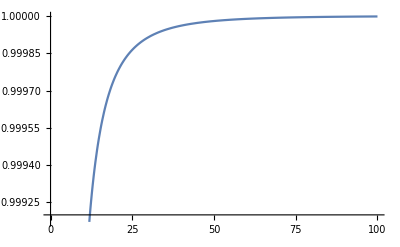

```mathematica
Pl201=ListInterpolation[Re[LDis1],{{0,100}}];
Plot[Pl201[y],{y,0,100}]
```

```mathematica
Pl21=ListInterpolation[Re[LDis22],{{0,80}}];
Pl22=ListInterpolation[Re[LDis32],{{80,160}}];
Pl24=ListInterpolation[Re[LDis5],{{0,100}}];
```

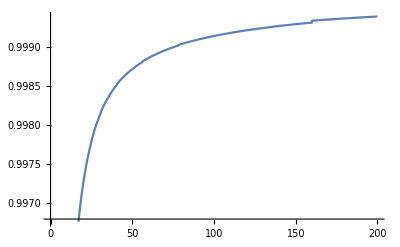

```mathematica
Fd[y_]:=Which[y<80,Pl21[y],80≤y≤160,Pl22[y],y>160,1-λ[y,200]^2];
Plot[Fd[y],{y,0,200}]
```

```mathematica
Fd2[y_]:=If[y<99,Pl24[y],1];
Plot[{Fd[y],Fd2[y],Pl201[y],1-λ[y,200]^2,1},{y,0,100},PlotRange->{0.997,1.0005},PlotStyle->{Black,Black,{Black,Dashed},{Black,Dotted,Thick},{Black,Dotted}},Frame->True,PlotRangePadding->0,FrameStyle->Thick,RotateLabel->False,FrameLabel->{(q_┴)^2/(4 m^2),(q_║)^2/(4 m^2)},LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```

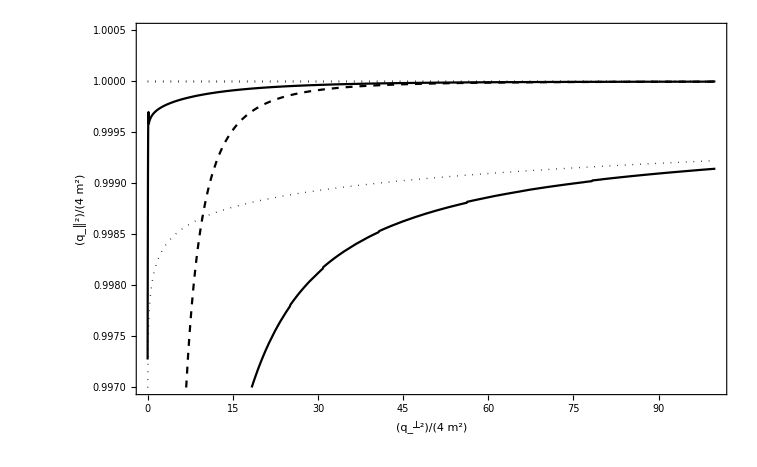

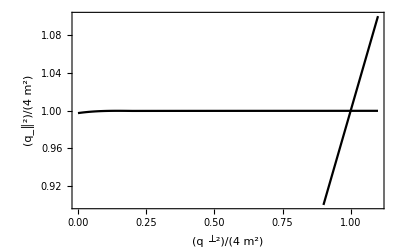

```mathematica
Plot[{y,Fd2[y]},{y,0,1.1},PlotRange->{0.9,1.1},PlotStyle->{Black},Frame->True,PlotRangePadding->0,FrameStyle->Thick,RotateLabel->False,FrameLabel->{(q_┴)^2/(4 m^2),(q_║)^2/(4 m^2)},LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```

## Graph for W2-11 in plasma

```mathematica
F[x_]:=2Log[x]-1+1/x^2;
W1[x_]:=π/4(H[x,Fd[x],200])^2 Fd[x]/x^0.5 F[(x/Fd[x])^0.5](1+(α*200)/(2*π)*dH[x,Fd[x],200])^-1 UnitStep[x-Fd[x]];
W2[x_]:=π/4(H[x,Fd2[x],200])^2 Fd2[x]/x^0.5 F[(x/Fd2[x])^0.5](1+(α*200)/(2*π)*dH[x,Fd2[x],200])^-1 UnitStep[x-Fd2[x]];
```

```mathematica
FindRoot[0.99941-Fd[y],{y,0}]
```

{y→213.101}

```mathematica
{{0.2,0.150713557587656},{0.3,0.2855144225974879},{0.4,0.42855385263692625},{0.5,0.5840985318363338},{0.6,0.7601484860164072},{0.7,0.9739743227674355},{0.8,1.2724332813784904},{0.9,1.8568641502700236},{0.95,2.6762257096515274},{0.99,7.0675798328796375}};
```

```mathematica
W1[x_,y_]:=π/4(H[x,y,200])^2 y/x^0.5 F[(x/y)^0.5](1+(α*200)/(2*π)*dH[x,y,200])^-1 UnitStep[y-x];
```

```mathematica
W1[0.99941,213.10125103556075]
```

Power::infy: Infinite expression 1/0. encountered.

0.

```mathematica
78.88288802097831
```

78.8829

```mathematica
List1={{0.4^0.5,0.000013901686385067311},{0.6^0.5,0.0006863717889706432},{0.7^0.5,0.002480935687515901},{0.8^0.5,0.008830720311548981},{0.9^0.5,0.04027413533874314},{0.95^0.5,0.12848472969240585},{0.99^0.5,1.2774129133017071},{0.999^0.5,50.26251531614401},{0.9992^0.5,69.97929671211607},{0.9993^0.5,78.88288802097831},{0.9994^0.5,71.50272770657683}};
```

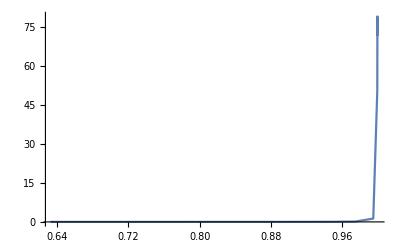

```mathematica
ListLinePlot[List1]
```